### Categorization

Tutorial

ErrorPlot

ErrorPlot`

ErrorPlot/tutorial/Plotting data with error bars

### Keywords

Details

# Plotting data with error bars

The ErrorPlot package allows for plotting data with errors in a flexible way.

ErrorPlot[{pt_1,pt_2,...}] | plot a data serie of points pt_i whose information is in the format specified by option DataFormat
 ErrorPlot[{pt_(1,1),pt_(1,2),...},{pt_(2,1),...},...] | plot various data series
ErrorLogPlot,ErrorLogLinearPlot,ErrorLogLogPlot | logarithmic scale analogous

Plotting data with errors.

First, we need to load the ErrorPlot package:

```mathematica
Needs["ErrorPlot`"]
```

As an example we will think of sampling the function x^2 in an interval [x,x+1], then the estimate for the function is ∫_x^(x+1) t^2 ⅆt and the error can be estimated with two times the standard deviation: σ=√(∫_x^(x+1) t^4 ⅆt-(∫_x^(x+1) t^2 ⅆt)^2).

```mathematica
data=Table[{x,x+1,Integrate[t^2,{t,x,x+1}],2*Sqrt[Integrate[t^4,{t,x,x+1}]-Integrate[t^2,{t,x,x+1}]^2]},{x,1,20,5}];
TableForm[data,TableHeadings->{None,{"x_min","x_max","y","δy"}}]
```

x_min | x_max | y | δy
1 | 2 | 7/3 | (2 √(34/5))/3
6 | 7 | 127/3 | (2 √(634/5))/3
11 | 12 | 397/3 | (16 √(31/5))/3
16 | 17 | 817/3 | (4 √(1021/5))/3

As the format of the data fits the automatic behavior of option DataFormat it can be plotted inmediately:

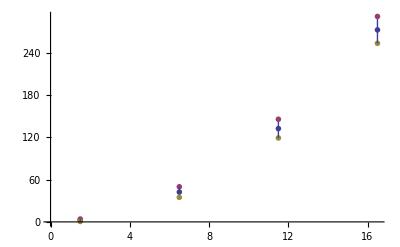

```mathematica
ErrorPlot[data]
```

Plotting various series of data is also straightfoward. This time we will plot also error bars in the x-axis:

```mathematica
data2=Table[{x,x+1,Integrate[t^2,{t,x,x+1}],2*Sqrt[Integrate[t^4,{t,x,x+1}]-Integrate[t^2,{t,x,x+1}]^2]},{x,3,20,5}];
```

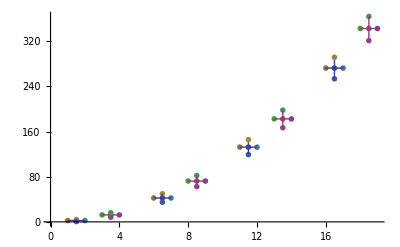

```mathematica
ErrorPlot[{data,data2},PlotErrorBars->{True,True}]
```

## Advanced manipulation of markers

Error bar ticks are plotted as markers and can thus be used in plot options.
First all point series are plotted in order and then each error bar edge points are plotted with the following conventional ordenation: first the points, then vertical bars top-down and then horizontal bars left-right:

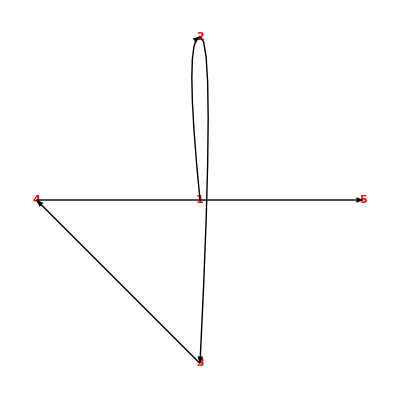

```mathematica
Graphics[{Red,Text[Style["1",Large,Bold],{0,0}],Text[Style["2",Large,Bold],{0,1}],Text[Style["3",Large,Bold],{0,-1}],Text[Style["4",Large,Bold],{-1,0}],Text[Style["5",Large,Bold],{1,0}],Black,Arrowheads[0.07],Arrow[BezierCurve[{{0,0},{-0.1,1},{0,1}}]],Arrow[BezierCurve[{{0,1},{0.1,1},{0,-1}}]],
Arrow[{{0,-1},{-1,0}}],Arrow[{{-1,0},{1,0}}]}]
```

By the use of option PlotMarkers we can fully customize them. The following example may make clearer the order in which each marker series is plot (for two data series):

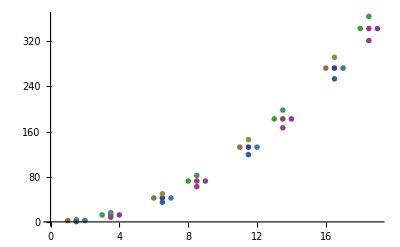

```mathematica
ErrorPlot[{data,data2},DataFormat->{"xMin","MaxX","y","dy"},PlotErrorBars->{True,True},PlotMarkers->Table[Graphics[{Text[i,{0,0}]}],{i,1,10}],HorizontalBarStyle->Transparent,VerticalBarStyle->{Transparent}]
```

Beware that points that are not demanded to plot are not numbered:

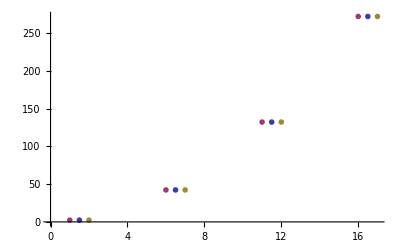

```mathematica
ErrorPlot[data,DataFormat->{"xMin","MaxX","y","dy"},PlotErrorBars->{True,False},PlotMarkers->Table[Graphics[{Text[i,{0,0}]}],{i,1,3}],HorizontalBarStyle->Transparent,VerticalBarStyle->{Transparent}]
```

For most common needs it is sufficient to use option PointMarkers to customize the points' appearance and ErrorBarTickSize and ErrorBarTickStyle for the error bars' ticks:

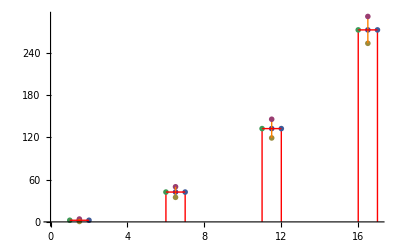

```mathematica
ErrorPlot[data,DataFormat->{"xMin","MaxX","y","dy"},PointMarkers->Graphics[{Orange,PointSize[Large],Point[{0,0}]}],PlotErrorBars->{True,True},Filling->{4->Axis,5->Axis},FillingStyle->Directive[Thick,Red],HorizontalBarStyle->{Directive[Thick,Red]},ErrorBarTickSize->{0,0.03},VerticalBarStyle->{Directive[Thick,Orange]},ErrorBarTickStyle->Orange]
```

Beware the use of PlotMarkers will make those options ignored:

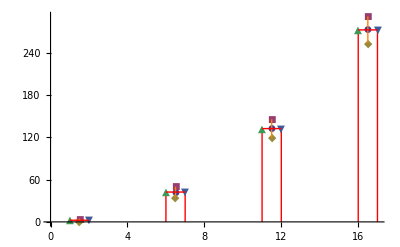

```mathematica
ErrorPlot[data,DataFormat->{"xMin","MaxX","y","dy"},PlotMarkers->Automatic,PointMarkers->Graphics[{Orange,PointSize[Large],Point[{0,0}]}],PlotErrorBars->{True,True},Filling->{4->Axis,5->Axis},FillingStyle->Directive[Thick,Red],HorizontalBarStyle->{Directive[Thick,Red]},ErrorBarTickSize->{0,0.03},VerticalBarStyle->{Directive[Thick,Orange]},ErrorBarTickStyle->Orange]
```

## Choosing the data's format

Users may prefer some format for the data such that it meets their personal criteria on intuitiveness, thus representing an interval by it's end points or by the central point and the radius, either absolute or relative. Package ErrorPlot is designed to be subjected to such choice, instead of having to convert the data to a different format.

As an example, we can show the three representations on the interval of the x variable are equivalent:

```mathematica
fullData=Table[{i[[1]],i[[2]],(i[[2]]+i[[1]])/2,(i[[2]]-i[[1]])/2,(i[[2]]-i[[1]])/(i[[2]]+i[[1]]),i[[3]],i[[4]]},{i,data}];
TableForm[fullData,TableHeadings->{None,{"x_min","x_max","x","dx","relx","y","δy"}}]
```

x_min | x_max | x | dx | relx | y | δy
1 | 2 | 3/2 | 1/2 | 1/3 | 7/3 | (2 √(34/5))/3
6 | 7 | 13/2 | 1/2 | 1/13 | 127/3 | (2 √(634/5))/3
11 | 12 | 23/2 | 1/2 | 1/23 | 397/3 | (16 √(31/5))/3
16 | 17 | 33/2 | 1/2 | 1/33 | 817/3 | (4 √(1021/5))/3

```mathematica
ErrorPlot[fullData[[All,{1,2,6,7}]],DataFormat->{"xMin","xMax","y","dy"},PlotErrorBars->True]
```

-Graphics-

```mathematica
ErrorPlot[fullData[[All,{3,4,6,7}]],DataFormat->{"x","dx","y","dy"},PlotErrorBars->True]
```

-Graphics-

```mathematica
ErrorPlot[fullData[[All,{3,5,6,7}]],DataFormat->{"x","relx","y","dy"},PlotErrorBars->True]
```

-Graphics-

DataFormat is prepared to recognize some variations on the strings defining the format so the user doesn't to care about it. See its page for more information.

More About

DataFormat

ErrorPlot

Related Tutorials

Data Visualization

Related Wolfram Education Group Courses